## Training Net

Helpers to compute the Jacobian (of a function at a point) and LogDet (of a matrix):

```mathematica
(* Takes input of and outputs a Jacobian and a corresponding function*)
JacobianNet[func_, epsilon_:1*^-4]:= Module[
	{n, lin, net1,sharedFunc}, 
	n = NetExtract[func, "Input"];
	net1 = NetGraph[{ReplicateLayer[n], ConstantArrayLayer["Array" -> N[epsilon]*IdentityMatrix[n]], TotalLayer[]},{{1, 2} -> 3}];
	sharedFunc = NetInsertSharedArrays[func];
	NetGraph[<|
		"addEpsilon"-> net1,
		"MapFunction" -> NetMapOperator[sharedFunc],
		"Function" -> sharedFunc,
		"subtract" -> NetMapThreadOperator[
			ThreadingLayer[Subtract,"Inputs"->2],<|"1"->1|>],
			"divideByEps" -> ElementwiseLayer[# / epsilon &],
			"transpose" -> TransposeLayer[]
		|>,
		{
			"addEpsilon" -> "MapFunction",
			{"MapFunction","Function"}->"subtract" -> "divideByEps" -> "transpose",
			"Function" -> NetPort["z"]
		}] 
];

(* 
Input:
Jacobian: nxn array
k: number of power series
Output:

*)
LogDet[n_,  k_:3] := Module[
	{powers, parts, elementwise, chains, diagonalElements, trace},
	(* Extract the dimension of the matrix *)
	(* (1) Find the power series expansion of log of the matrix *)
	(* Create k powers of the matrix *)
	powers = NetGraph[
		{ReplicateLayer[k-1], NetFoldOperator[DotLayer["Inputs" -> {{n, n}, {n, n}}], {"Output" -> "1"}],PrependLayer[]},
		{1 -> 2, NetPort["Input"] -> NetPort[2, "1"], {2, NetPort["Input"]} -> 3}	];
	parts = Table[PartLayer[i], {i, 1, k}];
	(* Combine powers of Jacobian with the coefficients of power series of log*)
	elementwise = Table[ElementwiseLayer[#/(i*(-1)^(i+1)) &], {i, 1, k}];
	chains = NetChain /@ Transpose[{parts, elementwise}];
	(* Sum the powers and combine with the corresponding coefficients to get the power series expansion *)
	powers = NetGraph[Join[chains, {powers, TotalLayer[]}], {k + 1 -> Range[k], Range[k] -> k+2}];
	(* (2) Take the trace of the power series*)
	diagonalElements = Table[PartLayer[{i, i}], {i, 1, n}];
	trace = NetGraph[Join[diagonalElements, {TotalLayer[]}], {Range[n] -> n+1}, "Input" -> {n, n}];
	NetChain[{powers,trace}]
	(*NetGraph[{ConstantArrayLayer["Array" -> IdentityMatrix[n]], powers, DotLayer[], SummationLayer[]}, {{1, 2} -> 3, 3 -> 4}*)
	(*, "Input" -> {n, n}*)
];
```

```mathematica
LogDet[2,2][{{1,2},{3,4}}]
```

-9.5

```mathematica
LogDet[Length[NetExtract[JacobianNet[forward],"Output"]]]
```

NetGraph[<>]

```mathematica
LogDet[2,2]
```

NetGraph[<>]

```mathematica
{{3,-2},{-4,6}}//MatrixForm
```

(3 | -2
-4 | 6)

```mathematica
(1+x1)^2+x2^2+x3^2+(1+x4)^2
```

```mathematica
Norm[({{1, 0}, {0, 1}})+({{3, 4}, {-4, 6}})]//N
```

8.30074

```mathematica
Det[IdentityMatrix[2]+({{0.4, 0.2}, {0.3, 0.5}})]
```

2.04

```mathematica
m=IdentityMatrix[2]+({{-0.2, 0.1}, {0.1, -0.3}})*10^-2
```

{{0.998,0.001},{0.001,0.997}}

```mathematica
Det[m]
```

0.995005

```mathematica
Log[Abs[Det[m]]]
```

-0.00500752

```mathematica
Norm[m]
```

0.998618

```mathematica
LogDet[2,2]
```

PartLayer::invindata2: Data supplied to port "Input" was not an array of rank ≥ 1 (or a list of these).

NetGraph::netinvnodes: $Failed is not a layer, a net, or a valid specification for one.

$Failed

```mathematica
LogDet[2][m-IdentityMatrix[2]]
```

-0.00500752

```mathematica
MatrixLog[m]//Tr
```

-1.96611

```mathematica
Total[Table[(-1)^(i+1)MatrixPower[m-IdentityMatrix[2],i]/i,{i,1,2}]]//Tr
```

-0.0050075

```mathematica
createPowerNet[2,2][m-IdentityMatrix[2]]//Tr
```

-0.0050075

## PROBLEM TO SOLVE!

```mathematica
LogDet[2,3][{{3,-2},{-4,6}}]
```

10.5

```mathematica
N@Log@Abs@Det[{{3,-2},{-4,6}}]
```

2.30259

```mathematica
MatrixLog[{{3,-2},{-4,6}}]//Tr//N
```

2.30259

An example forward net

```mathematica
wrapInResidual[net_] := NetGraph[{net,TotalLayer[]},{{NetPort["Input"],1}->2}]
```

```mathematica
forward = NetInitialize@NetChain[Table[wrapInResidual[NetChain[{2,ElementwiseLayer["ELU"]}]], 3]]
```

NetChain[<>]

```mathematica
Length[NetExtract[JacobianNet[forward],"Output"]]
```

2

```mathematica
LogDet[Length[NetExtract[JacobianNet[forward],"Output"]]]
```

NetGraph[<>]

NetGraph[<>]

```mathematica
JacobianNet[forward]
```

NetGraph[<>]

The loss function is:

```mathematica
trainingnet = NetGraph[<|
	"Jacobian" -> JacobianNet[forward],
	"LogDet" -> LogDet[Length[NetExtract[JacobianNet[forward],"Output"]]], (* TODO: REPLACE ME BY THE STUFF *)
	"norm" -> DotLayer[],
	"total" -> TotalLayer[],
	"minus" ->  ElementwiseLayer[-#&],
	"MinusIdentity" -> ConstantPlusLayer["Biases" -> -IdentityMatrix[Length[NetExtract[JacobianNet[forward],"Output"]]]]
|>,
	{NetPort[{"Jacobian", "Output"}] ->"MinusIdentity" -> "LogDet" -> "minus",
	{NetPort[{"Jacobian", "z"}], NetPort[{"Jacobian", "z"}]} -> "norm",
	{"minus", "norm"} -> "total" -> NetPort["Loss"]}
]
```

NetGraph[<>]

```mathematica
trainingnet
```

$Failed

#### Data from Gaussian

```mathematica
data=RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}],1000];
```

```mathematica
normdata=data/Norm[data];
```

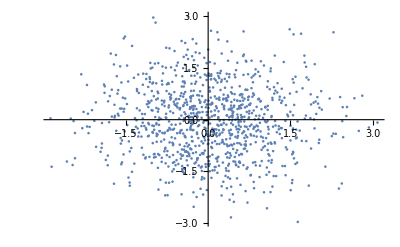

```mathematica
ListPlot@data
```

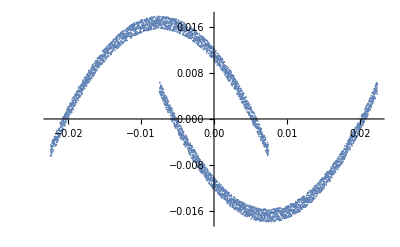

```mathematica
ListPlot@normdata
```

Don’t forget to freeze the parts that have to be fixed when training:

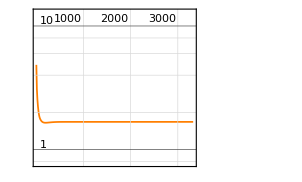
NetTrain Results
summary | ,,  batches:33260  rounds:3326  time:27s  examples/s:80188
data | ,,  training examples:629  processed examples:2128640  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.68
 | rounds
loss | -Graphics- | 
 |

```mathematica
trainingresult=NetTrain[trainingnet, <|"Input"->data|>, All, LearningRateMultipliers -> {{"Jacobian","addEpsilon"}->None,"MinusIdentity"->None},Method->{"ADAM","L2Regularization"->0.5}]
```

```mathematica
ld=LearnDistribution[data,Method->{"RealNVP"}]
```

LearnedDistribution[…]

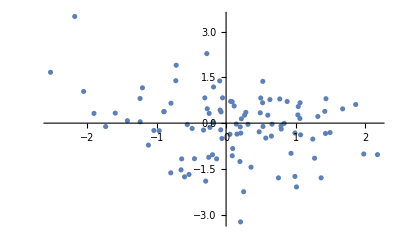

```mathematica
RandomVariate[ld,100]//ListPlot
```

## To do

Train network with LearnDistribution with method realNVP on MNIST

Extract Sampler and ProbabilityNet

Use ProbabilityNet as a feature extractor

Feature vector from data should have a normal distribution

Give data that is not original distribution so you should have something different so you can learn this distribution using LearnDistribution - but not with RealNVP

Idea is to learn a simple distribution

Get new data → pass it through probability net → this gives features → then learn distribution on these features →If you want to sample, just sample on feature space and pass it through Sampler net

For example, train on digits 0 to 8, then give ProbabilityNet digit 9. Then you LearnDistribution of these features

#### Transfer Learning

Suppose you have a network that is trained on a lot of data.

Take a network, trained on big dataset, as a feature extractor of the new data you want to learn from.

Then you learn the classifier in the feature space.

Extract Z_out from coupling_2

high level features are in Z_out

Z_out is a vector of size 728 with MNIST. Ask amir if important features are at the end or the beginning.

Recreate a vector of size 728 and pass it through Sampler

```mathematica
ld⟦1,"Model"⟧
```

<|Sampler→NetGraph[<>],Processor→Center,PostProcessor→FirstValues,ProbabilityNet→NetGraph[<>],Method→RealNVP,Options→<|MaxTrainingRounds→<|Value→500,Options→<||>|>,ActivationFunction→<|Value→Ramp,Options→<||>|>,NetworkDepth→<|Value→2,Options→<||>|>,CouplingLayersNumber→<|Value→2,Options→<||>|>,NetworkType→<|Value→FullyConnected,Options→<||>|>|>|>

```mathematica
ld⟦1,"Model","ProbabilityNet"⟧
```

NetGraph[<>]

Extract the trained net

```mathematica
trainingresult["TrainedNet"]
```

NetGraph[<>]

```mathematica
trainednet=NetExtract[trainingresult["TrainedNet"], {"Jacobian", "Function"}]
```

NetChain[<>]

This is a shit to be fixed by Jerome (because of shared arrays)

```mathematica
trainednet[{0,0}]
```

{6.82261,8.58343}

## Sampling with the training Net

Here we invert the network to be able to sample the input, given an output generated from a multidimensional Normal distribution:

```mathematica
invertResidualNetwork[net_, iter_] := Module[
	{functions, invcores},
	functions = NetExtract[net, {All, 1}]; (* Extract residual blocks *)
	invcores = NetGraph[
		{#, ThreadingLayer[Subtract]},
		{NetPort["state"] -> 1, NetPort["y"] -> NetPort[2, 1], 1 -> NetPort[2, 2]}
	] & /@ functions; (* *)
	invcores = NetFoldOperator[#, {"Output" -> "state"}] & /@ invcores;
	invcores = NetChain[{ReplicateLayer[iter], #, SequenceLastLayer[]}] & /@ invcores;
	NetJoin @@ Reverse[invcores]
];
```

Test the function:

```mathematica
inverse=invertResidualNetwork[forward,5]
out=forward[{1,2}]
inverse[out]
```

NetChain[<>]

{0.679889,0.674352}

{0.973546,2.06636}

Upsy. It seems that the inverse is not working on the trained net (lost property?)

```mathematica
inverse=invertResidualNetwork[trainednet,5]
out=trainednet[{1,2}]
inverse[out]
```

NetChain[<>]

{5.98738,2.84972}

{-0.168378,5.8367}

```mathematica
inverse=invertResidualNetwork[trainednet,5]
randomoutput=Table[RandomVariate[NormalDistribution[]],2]
randominput= inverse[randomoutput]
trainednet[randominput]
```

NetChain[<>]

{0.299434,0.298762}

{-124664.,-9.34082×10^6}

{-124667.,1.33778×10^7}

```mathematica
randomoutput=Table[RandomVariate[NormalDistribution[]],2]
randominput= trainedsampler[randomoutput]
trainednet[randominput]
```

{0.610261,0.0506235}

{-35333.4,-0.479209}

{2.56605×10^6,2.74666×10^6}